```mathematica
data = Import["E:\\2019spr\\近代物理实验\\MyReport\\0426_cidianzu\\para1.txt","Table"];
```

```mathematica
data2 =  Import["E:\\2019spr\\近代物理实验\\MyReport\\0426_cidianzu\\para2.txt","Table"];
data2=Delete[data2,-1]; (* remove extra {} *)
```

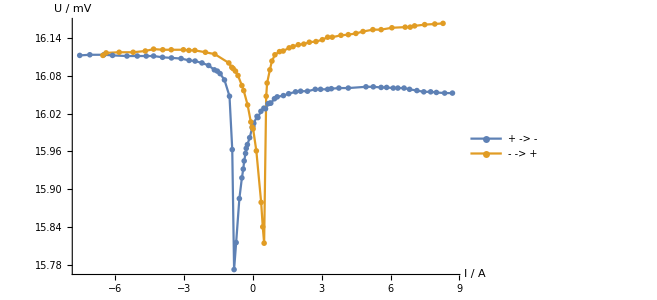

```mathematica
ListLinePlot[{data,data2},AxesLabel->{"I / A","U / mV"},PlotLegends->Placed[{"+ -> -","- -> +"},{0.8,0.4}],PlotMarkers->{●,x}]
```

```mathematica
data3 =Import["E:\\2019spr\\近代物理实验\\MyReport\\0426_cidianzu\\perp1.txt","Table"];
```

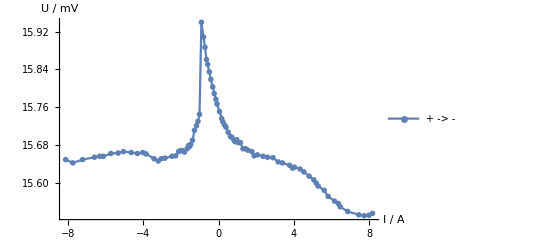

```mathematica
fig1 = ListLinePlot[data3,AxesLabel->{"I / A","U / mV"},PlotLegends->Placed[{"+ -> -"},{0.8,0.8}],PlotMarkers->{●},AspectRatio->0.6]
```